# Notebook for : Gravitational Waves Volume I: Theory and Experiments by Michele Maggiore

Geoff Cope
University of Utah
August 28th, 2021

```mathematica
(*
Page 334 Volume 2 is where you want to find the sensitivity curve
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book Description

```mathematica
Hyperlink["Gravitational Waves Volume I: Theory and Experiments by Michele Maggiore",
"https://oxford.universitypressscholarship.com/view/10.1093/acprof:oso/9780198570745.001.0001/acprof-9780198570745"]
```

[Gravitational Waves Volume I: Theory and Experiments by Michele Maggiore](https://oxford.universitypressscholarship.com/view/10.1093/acprof:oso/9780198570745.001.0001/acprof-9780198570745)

```mathematica
Hyperlink["Gravitational Waves – Volume 2: Astrophysics and Cosmology",
"https://oxford.universitypressscholarship.com/view/10.1093/oso/9780198570899.001.0001/oso-9780198570899"]
```

[Gravitational Waves – Volume 2: Astrophysics and Cosmology](https://oxford.universitypressscholarship.com/view/10.1093/oso/9780198570899.001.0001/oso-9780198570899)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 7 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Chapter 1

```mathematica
Clear[δ]
δ[i_,j_]:= KroneckerDelta[i,j]
```

```mathematica
(* Equation 1.35 Page 9 *) 
Clear[P]
P[n_]:= 
Table[δ[i,j] - n[[i]] n[[j]] , {i,1,3},{j,1,3} ]
```

```mathematica
(* Using the n on page 110 *) 
Clear[n]
n = {0,0,1}
```

{0,0,1}

```mathematica
{0,0,1}
```

{0,0,1}

```mathematica
Table[ Sum[ n[[i]] P[n][[i,j]] , {i,1,3} ] , {j,1,3} ]  (* Is tranverse *)
```

{0,0,0}

```mathematica
(* Is a projector *) 
Table[ 
Sum[ 
P[n][[i,k]] P[n][[k,j]]  , {k,1,3} ]  , 
{i,1,3},{j,1,3} ]  // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)

```mathematica
(* Is a projector *) 
P[n] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)

```mathematica
(* Has a trace of 2 *) 
Tr[P[n] ]
```

2

```mathematica
(* Equation 1.36 Page 9 *) 
Clear[Λ]
Λ[n_]:= 
Table[
P[n][[i,k]]  P[n][[j,l]] - 1/2 P[n][[i,j]]  P[n][[k,l]]  , 
{i,1,3},{j,1,3},{k,1,3},{l,1,3} ]
```

```mathematica
Λ[n] // MatrixForm
```

((1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (-1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
Table [ Λ[n][[i,j,k,l]]  ,  {i,1,3},{j,1,3},{k,1,3},{l,1,3}  ]  // MatrixForm
```

((1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (-1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
(* Figure out why this doesn't work *) 
(*
Table[ 
Sum[ Λ[n][[i,j,k,l]] Λ[n][[k,l,m,n]] , {k,1,3} , {l,1,3} ]   , 
 {i,1,3},{j,1,3},{m,1,3},{n,1,3}  ]  ;
*)
```

```mathematica
(* Is tranverse on all indices *) 
Table[
Sum[
n[[i]] Λ[n][[i,j,k,l]]  , 
{i,1,3}]   , 
{j,1,3},{k,1,3},{l,1,3} ]   // MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
(* Is tranverse on all indices *) 
Table[
Sum[
n[[j]] Λ[n][[i,j,k,l]]  , 
{j,1,3}]   , 
{i,1,3},{k,1,3},{l,1,3} ]   // MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
(* Is tranverse on all indices *) 
Table[
Sum[
n[[k]] Λ[n][[i,j,k,l]]  , 
{k,1,3}]   , 
{i,1,3},{j,1,3},{l,1,3} ]   // MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
(* Is tranverse on all indices *) 
Table[
Sum[
n[[l]] Λ[n][[i,j,k,l]]  , 
{l,1,3}]   , 
{i,1,3},{j,1,3},{k,1,3} ]   // MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
(* Check this later *) 
(* Equation 1.39 page 10 *) 
Clear[Λ]
Λ[n_]:= Table[ 
δ[i,k] δ[j,l] - 1/2 δ[i,j] δ[k,l]  - n[[j]] n[[l]] δ[i,k] - n[[i]] n[[k]] δ[j,l] +1/2 n[[k]] n[[l]] δ[i,j] +1/2 n[[i]] n[[j]] δ[k,l] +1/2 n[[i]] n[[j]] n[[k]] n[[l]]  , 
{i,1,3},{j,1,3},{k,1,3} ,{l,1,3} ]
```

```mathematica
Λ[n] // MatrixForm
```

((1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (-1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

## Chapter 2

```mathematica
(* Page 96 *) 
Clear[Λrot]
Λrot = 
({{Cos[ψ], -Sin[ψ]}, {Sin[ψ], Cos[ψ]}}) ;
Λrot // MatrixForm
```

(Cos[ψ] | -Sin[ψ]
Sin[ψ] | Cos[ψ])

```mathematica
Clear[h,𝒽]
𝒽 =
 ({{SubPlus[h], Subscript[h,x]}, {Subscript[h,x], -SubPlus[h]}}) ;
𝒽 // MatrixForm
```

(h_+ | h_x
h_x | -h_+)

```mathematica
Clear[eq2pt192]
eq2pt194 = 
Table[ Sum[ Λrot[[a,c]]Λrot[[b,d]] 𝒽[[c,d]] , {c,1,2},{d,1,2}] , {a,1,2},{b,1,2} ]  // Expand // Simplify  ;
eq2pt194 // MatrixForm
```

(Cos[2 ψ] h_+-Sin[2 ψ] h_x | Sin[2 ψ] h_++Cos[2 ψ] h_x
Sin[2 ψ] h_++Cos[2 ψ] h_x | -Cos[2 ψ] h_++Sin[2 ψ] h_x)

## Chapter 3

```mathematica
(* Page 110 *) 
Clear[M]
M = 
({{M11[t], M12[t], M13[t]}, {M12[t], M22[t], M23[t]}, {M13[t], M23[t], M33[t]}}) ;
M // MatrixForm
```

(M11[t] | M12[t] | M13[t]
M12[t] | M22[t] | M23[t]
M13[t] | M23[t] | M33[t])

```mathematica
D[ M , {t,2} ]  // MatrixForm
```

(M11''[t] | M12''[t] | M13''[t]
M12''[t] | M22''[t] | M23''[t]
M13''[t] | M23''[t] | M33''[t])

```mathematica
(* Equation 3.61 Page 110 *) 
P[n] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)

```mathematica
(* Equation 3.58 page 109 *) 
(* No idea if this is right CHECK THIS *) 
Clear[Q]
Q[M_]:= 
Table[ M[[i,j]] - 1/3 δ[i,j] Sum[ M[[k,k]], {k,1,3}]   , {i,1,3},{j,1,3} ]  // Expand // Simplify
```

```mathematica
Q[M] // MatrixForm
```

(1/3 (2 M11[t]-M22[t]-M33[t]) | M12[t] | M13[t]
M12[t] | 1/3 (-M11[t]+2 M22[t]-M33[t]) | M23[t]
M13[t] | M23[t] | 1/3 (-M11[t]-M22[t]+2 M33[t]))

```mathematica
(* Equation 3.64 Page 110 *) 
Clear[eq3pt64]
eq3pt64 = 
Table[
Sum[
Λ[n][[i,j,k,l]] D[M,{t,2}][[k,l]] , {k,1,3} , {l,1,3} ] ,{i,1,3},{j,1,3} ]   ;
eq3pt64// MatrixForm
```

(M11''[t]/2-M22''[t]/2 | M12''[t] | 0
M12''[t] | -1/2 M11''[t]+M22''[t]/2 | 0
0 | 0 | 0)

```mathematica
Clear[eq3pt65]
eq3pt65 = 
((2 G)/(r c^4)) eq3pt64[[1,1]] // Expand // Simplify
```

(G (M11''[t]-M22''[t]))/(c^4 r)

```mathematica
eq3pt65 /. t-> t-r/c
```

(G (M11''[-r/c+t]-M22''[-r/c+t]))/(c^4 r)

```mathematica
Clear[eq3pt66]
eq3pt66 = 
 ((2 G)/(r c^4)) eq3pt64[[1,2] ]// Expand // Simplify
```

(2 G M12''[t])/(c^4 r)

```mathematica
eq3pt66 /. t-> t-r/c
```

(2 G M12''[-r/c+t])/(c^4 r)

```mathematica
(* Equation 3.70 Page 111 *) 
Clear[R]
R = 
({{Cos[ϕ], Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}}) . ({{1, 0, 0}, {0, Cos[θ], Sin[θ]}, {0, -Sin[θ], Cos[θ]}})  ;
R // MatrixForm
```

(Cos[ϕ] | Cos[θ] Sin[ϕ] | Sin[θ] Sin[ϕ]
-Sin[ϕ] | Cos[θ] Cos[ϕ] | Cos[ϕ] Sin[θ]
0 | -Sin[θ] | Cos[θ])

```mathematica
Clear[Mprime]
Mprime = 
Transpose[R]  . M  . R  // Expand // Simplify  ;
Mprime// MatrixForm
```

(Cos[ϕ]^2 M11[t]+Sin[ϕ] (-2 Cos[ϕ] M12[t]+M22[t] Sin[ϕ]) | Cos[θ] Cos[2 ϕ] M12[t]-Cos[ϕ] M13[t] Sin[θ]+(Cos[θ] Cos[ϕ] M11[t]-Cos[θ] Cos[ϕ] M22[t]+M23[t] Sin[θ]) Sin[ϕ] | Cos[θ] Cos[ϕ] M13[t]+Cos[2 ϕ] M12[t] Sin[θ]-(Cos[θ] M23[t]+Cos[ϕ] (-M11[t]+M22[t]) Sin[θ]) Sin[ϕ]
Cos[θ] Cos[2 ϕ] M12[t]-Cos[ϕ] M13[t] Sin[θ]+(Cos[θ] Cos[ϕ] M11[t]-Cos[θ] Cos[ϕ] M22[t]+M23[t] Sin[θ]) Sin[ϕ] | Cos[θ]^2 Cos[ϕ]^2 M22[t]-2 Cos[θ] Cos[ϕ] M23[t] Sin[θ]+M33[t] Sin[θ]^2-2 Cos[θ] M13[t] Sin[θ] Sin[ϕ]+Cos[θ]^2 M11[t] Sin[ϕ]^2+Cos[θ]^2 M12[t] Sin[2 ϕ] | Cos[2 θ] Cos[ϕ] M23[t]+Cos[θ] Cos[ϕ]^2 M22[t] Sin[θ]-Cos[θ] M33[t] Sin[θ]+Cos[θ]^2 M13[t] Sin[ϕ]+2 Cos[θ] Cos[ϕ] M12[t] Sin[θ] Sin[ϕ]-M13[t] Sin[θ]^2 Sin[ϕ]+Cos[θ] M11[t] Sin[θ] Sin[ϕ]^2
Cos[θ] Cos[ϕ] M13[t]+Cos[2 ϕ] M12[t] Sin[θ]-(Cos[θ] M23[t]+Cos[ϕ] (-M11[t]+M22[t]) Sin[θ]) Sin[ϕ] | Cos[2 θ] Cos[ϕ] M23[t]+Cos[θ] Cos[ϕ]^2 M22[t] Sin[θ]-Cos[θ] M33[t] Sin[θ]+Cos[θ]^2 M13[t] Sin[ϕ]+2 Cos[θ] Cos[ϕ] M12[t] Sin[θ] Sin[ϕ]-M13[t] Sin[θ]^2 Sin[ϕ]+Cos[θ] M11[t] Sin[θ] Sin[ϕ]^2 | Cos[θ]^2 M33[t]+Cos[ϕ]^2 M22[t] Sin[θ]^2+Cos[ϕ] M23[t] Sin[2 θ]+M13[t] Sin[2 θ] Sin[ϕ]+M11[t] Sin[θ]^2 Sin[ϕ]^2+M12[t] Sin[θ]^2 Sin[2 ϕ])

```mathematica
Clear[mPrimeReplace]
mPrimeReplace = { 
D[M11[t],{t,2}]-> D[Mprime[[1,1]],{t,2}] , 
D[M12[t],{t,2}]-> D[Mprime[[1,2]],{t,2}] , 
D[M22[t],{t,2}]-> D[Mprime[[2,2]],{t,2}]
} ;
mPrimeReplace  // TableForm
```

M11''[t]→Cos[ϕ]^2 M11''[t]+Sin[ϕ] (-2 Cos[ϕ] M12''[t]+Sin[ϕ] M22''[t])
M12''[t]→Cos[θ] Cos[2 ϕ] M12''[t]-Cos[ϕ] Sin[θ] M13''[t]+Sin[ϕ] (Cos[θ] Cos[ϕ] M11''[t]-Cos[θ] Cos[ϕ] M22''[t]+Sin[θ] M23''[t])
M22''[t]→Cos[θ]^2 Sin[ϕ]^2 M11''[t]+Cos[θ]^2 Sin[2 ϕ] M12''[t]-2 Cos[θ] Sin[θ] Sin[ϕ] M13''[t]+Cos[θ]^2 Cos[ϕ]^2 M22''[t]-2 Cos[θ] Cos[ϕ] Sin[θ] M23''[t]+Sin[θ]^2 M33''[t]

```mathematica
Clear[eq3pt72a] (* Page 111 *) 
eq3pt72a = 
eq3pt65  /. mPrimeReplace // Expand // Simplify  (* I think this is right *)
```

1/(c^4 r)G ((Cos[ϕ]^2-Cos[θ]^2 Sin[ϕ]^2) M11''[t]-1/2 (3+Cos[2 θ]) Sin[2 ϕ] M12''[t]+Sin[2 θ] Sin[ϕ] M13''[t]-Cos[θ]^2 Cos[ϕ]^2 M22''[t]+Sin[ϕ]^2 M22''[t]+Cos[ϕ] Sin[2 θ] M23''[t]-Sin[θ]^2 M33''[t])

```mathematica
Clear[eq3pt72b] (* Page 111 *) 
eq3pt72b = 
eq3pt66 /. mPrimeReplace // Expand // Simplify (* I think this is right *)
```

(2 G (Cos[θ] Cos[ϕ] Sin[ϕ] M11''[t]+Cos[θ] Cos[2 ϕ] M12''[t]-Cos[ϕ] Sin[θ] M13''[t]-Cos[θ] Cos[ϕ] Sin[ϕ] M22''[t]+Sin[θ] Sin[ϕ] M23''[t]))/(c^4 r)

```mathematica
Clear[oscillatingMassSecondMoment]
oscillatingMassSecondMoment = 
Table[μ a^2((1+Cos[2ω t])/2) δ[i,3] δ[j,3] , {i,1,3},{j,1,3} ]  ;
oscillatingMassSecondMoment  // MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1/2 a^2 μ (1+Cos[2 t ω]))

```mathematica
Clear[oscillatingMassSecondMomentReplace]
oscillatingMassSecondMomentReplace = 
Table[ 
Flatten[D[ M , {t,2} ] ][[i]] -> 
Flatten[D[ oscillatingMassSecondMoment , {t,2}] ][[i]] , {i,1,9} ]   ;
oscillatingMassSecondMomentReplace// TableForm
```

M11''[t]→0
M12''[t]→0
M13''[t]→0
M12''[t]→0
M22''[t]→0
M23''[t]→0
M13''[t]→0
M23''[t]→0
M33''[t]→-2 a^2 μ ω^2 Cos[2 t ω]

```mathematica
Clear[eq3pt76] (* Page 113 *) 
eq3pt76 = 
(G/(5 c^5))( Sum[ D[ M , {t,3} ][[i,j]]D[ M , {t,3} ][[i,j]] , {i,1,3} , {j,1,3} ] +(-1/3)Sum[ (D[ M , {t,3} ][[k,k]])^2, {k,1,3} ] )
```

(G ((M11^(3)[t])^2+2 (M12^(3)[t])^2+2 (M13^(3)[t])^2+(M22^(3)[t])^2+2 (M23^(3)[t])^2+(M33^(3)[t])^2+1/3 (-(M11^(3)[t])^2-(M22^(3)[t])^2-(M33^(3)[t])^2)))/(5 c^5)

```mathematica
(* Not the same under interchange of i and j *) 
(* equation 3.149 Page 127 *) 
Clear[J]
J = 
({{J11[t], J12[t], J13[t]}, {J21[t], J22[t], J23[t]}, {J31[t], J32[t], J33[t]}}) ;
J // MatrixForm
```

(J11[t] | J12[t] | J13[t]
J21[t] | J22[t] | J23[t]
J31[t] | J32[t] | J33[t])

```mathematica
D[J,{t,2} ]  // MatrixForm
```

(J11''[t] | J12''[t] | J13''[t]
J21''[t] | J22''[t] | J23''[t]
J31''[t] | J32''[t] | J33''[t])

```mathematica
Clear[ε]
ε = LeviCivitaTensor[3] ;
ε // MatrixForm
```

((0
0
0) | (0
0
1) | (0
-1
0)
(0
0
-1) | (0
0
0) | (1
0
0)
(0
1
0) | (-1
0
0) | (0
0
0))

```mathematica
Clear[eq3pt151]
eq3pt151 = 
((4 G)/(3 r c^5)) Table[Sum[Λ[n][[i,j,k,l]] n[[m]] (ε[[m,k,p]] J[[p,l]] + ε[[m,l,p]] J[[p,k]] )   , {k,1,3} , {l,1,3}  ,{m,1,3},{p,1,3} ] ,{i,1,3},{j,1,3}]  ;
eq3pt151// MatrixForm
```

((4 G (J12[t]+J21[t]))/(3 c^5 r) | (4 G (-J11[t]+J22[t]))/(3 c^5 r) | 0
(4 G (-J11[t]+J22[t]))/(3 c^5 r) | (4 G (-J12[t]-J21[t]))/(3 c^5 r) | 0
0 | 0 | 0)

```mathematica
(* Need to make these time derivatives - find formula  *) 
Clear[eq3pt157]
eq3pt157 = 
D[ eq3pt151[[1,1]] , {t,2} ]
```

(4 G (J12''[t]+J21''[t]))/(3 c^5 r)

```mathematica
(* Need to make these time derivatives - find formula *) 
Clear[eq3pt158]
eq3pt158 = 
D[ eq3pt151[[1,2]], {t,2} ]
```

(4 G (-J11''[t]+J22''[t]))/(3 c^5 r)

```mathematica
R // MatrixForm
```

(Cos[ϕ] | Cos[θ] Sin[ϕ] | Sin[θ] Sin[ϕ]
-Sin[ϕ] | Cos[θ] Cos[ϕ] | Cos[ϕ] Sin[θ]
0 | -Sin[θ] | Cos[θ])

```mathematica
Clear[Jprime]
Jprime = 
Transpose[R] . D[J,{t,2} ] . R  // Expand // Simplify   ;
Jprime // MatrixForm
```

(Cos[ϕ]^2 J11''[t]-Sin[ϕ] (Cos[ϕ] J12''[t]+Cos[ϕ] J21''[t]-Sin[ϕ] J22''[t]) | Cos[θ] Cos[ϕ] Sin[ϕ] J11''[t]+Cos[θ] Cos[ϕ]^2 J12''[t]-Cos[ϕ] Sin[θ] J13''[t]-Cos[θ] Sin[ϕ]^2 J21''[t]-Cos[θ] Cos[ϕ] Sin[ϕ] J22''[t]+Sin[θ] Sin[ϕ] J23''[t] | Cos[ϕ] Sin[θ] Sin[ϕ] J11''[t]+Cos[ϕ]^2 Sin[θ] J12''[t]+Cos[θ] Cos[ϕ] J13''[t]-Sin[θ] Sin[ϕ]^2 J21''[t]-Cos[ϕ] Sin[θ] Sin[ϕ] J22''[t]-Cos[θ] Sin[ϕ] J23''[t]
Cos[θ] Cos[ϕ] Sin[ϕ] J11''[t]-Cos[θ] Sin[ϕ]^2 J12''[t]+Cos[θ] Cos[ϕ]^2 J21''[t]-Cos[θ] Cos[ϕ] Sin[ϕ] J22''[t]-Cos[ϕ] Sin[θ] J31''[t]+Sin[θ] Sin[ϕ] J32''[t] | Cos[θ]^2 Sin[ϕ]^2 J11''[t]+Cos[θ]^2 Cos[ϕ] Sin[ϕ] J12''[t]-Cos[θ] Sin[θ] Sin[ϕ] J13''[t]+Cos[θ]^2 Cos[ϕ] Sin[ϕ] J21''[t]+Cos[θ]^2 Cos[ϕ]^2 J22''[t]-Cos[θ] Cos[ϕ] Sin[θ] J23''[t]-Cos[θ] Sin[θ] Sin[ϕ] J31''[t]-Cos[θ] Cos[ϕ] Sin[θ] J32''[t]+Sin[θ]^2 J33''[t] | Cos[θ] Sin[θ] Sin[ϕ]^2 J11''[t]+Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ] J12''[t]+Cos[θ]^2 Sin[ϕ] J13''[t]+Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ] J21''[t]+Cos[θ] Cos[ϕ]^2 Sin[θ] J22''[t]+Cos[θ]^2 Cos[ϕ] J23''[t]-Sin[θ]^2 Sin[ϕ] J31''[t]-Cos[ϕ] Sin[θ]^2 J32''[t]-Cos[θ] Sin[θ] J33''[t]
Cos[ϕ] Sin[θ] Sin[ϕ] J11''[t]-Sin[θ] Sin[ϕ]^2 J12''[t]+Cos[ϕ]^2 Sin[θ] J21''[t]-Cos[ϕ] Sin[θ] Sin[ϕ] J22''[t]+Cos[θ] Cos[ϕ] J31''[t]-Cos[θ] Sin[ϕ] J32''[t] | Cos[θ] Sin[θ] Sin[ϕ]^2 J11''[t]+Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ] J12''[t]-Sin[θ]^2 Sin[ϕ] J13''[t]+Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ] J21''[t]+Cos[θ] Cos[ϕ]^2 Sin[θ] J22''[t]-Cos[ϕ] Sin[θ]^2 J23''[t]+Cos[θ]^2 Sin[ϕ] J31''[t]+Cos[θ]^2 Cos[ϕ] J32''[t]-Cos[θ] Sin[θ] J33''[t] | Sin[θ]^2 Sin[ϕ]^2 J11''[t]+Cos[ϕ] Sin[θ]^2 Sin[ϕ] J12''[t]+Cos[θ] Sin[θ] Sin[ϕ] J13''[t]+Cos[ϕ] Sin[θ]^2 Sin[ϕ] J21''[t]+Cos[ϕ]^2 Sin[θ]^2 J22''[t]+Cos[θ] Cos[ϕ] Sin[θ] J23''[t]+Cos[θ] Sin[θ] Sin[ϕ] J31''[t]+Cos[θ] Cos[ϕ] Sin[θ] J32''[t]+Cos[θ]^2 J33''[t])

```mathematica
(* This looks right *) 
Clear[eq3pt161]
eq3pt161 = 
hPlus ==(  (1/r)((4 G)/(3 c^5))( Jprime[[1,2]]+Jprime[[2,1]] )  // Expand  // FullSimplify   )
```

hPlus==(4 G (Cos[θ] Cos[2 ϕ] (J12''[t]+J21''[t])+Cos[θ] Sin[2 ϕ] (J11''[t]-J22''[t])-Cos[ϕ] Sin[θ] (J13''[t]+J31''[t])+Sin[θ] Sin[ϕ] (J23''[t]+J32''[t])))/(3 c^5 r)

```mathematica
(* Harder to tell, but I think this is equivalent *) 
Clear[eq3pt162]
eq3pt162 = 
hCross ==(  Collect[ ( (1/r)((4 G)/(3 c^5))( Jprime[[2,2]]-Jprime[[1,1]] )  // Expand // Simplify    ) , { Jprime[[1,1]] , Jprime[[2,2]] , Jprime[[3,3]] } ]  )
```

hCross==1/(3 c^5 r)G (-4 (Cos[ϕ]^2-Cos[θ]^2 Sin[ϕ]^2) J11''[t]+(3+Cos[2 θ]) Sin[2 ϕ] J12''[t]-4 (Cos[θ] Sin[θ] Sin[ϕ] J13''[t]-1/4 (3+Cos[2 θ]) Sin[2 ϕ] J21''[t]-Cos[θ]^2 Cos[ϕ]^2 J22''[t]+Sin[ϕ]^2 J22''[t]+Cos[θ] Cos[ϕ] Sin[θ] J23''[t]+Cos[θ] Sin[θ] Sin[ϕ] J31''[t]+Cos[θ] Cos[ϕ] Sin[θ] J32''[t]-Sin[θ]^2 J33''[t]))

```mathematica
(* Check this, no idea if this is right.  Also simplifying takes forever *) 
Clear[eq3pt163]
eq3pt163 = 
( D[ ( hPlus /. ( eq3pt161 /. Equal-> Rule  )  ) , t ]  )^2+( D[ ( hCross /. ( eq3pt162 /. Equal-> Rule  )  ) , t ] )^2 // Expand  ;
```

```mathematica
(* Do something like this first for averaging, go back and redo.  This doesn't work  *) 
Clear[eq3pt163Average]

(*
eq3pt163Average = 
(1/P)Integrate[ eq3pt163 , {t,0,P}]
*)
```

```mathematica
(* Do something like this first for integration, go back and redo *) 
(*
Integrate[ Sin[θ] eq3pt163Average , {ϕ,0,2π} , {θ,0,π} ] 
*)
```

```mathematica
Clear[eq3pt212]
eq3pt212 = 
SphericalHarmonicY[2,2,θ,ϕ]
```

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

```mathematica
Clear[eq3pt213]
eq3pt213 = 
SphericalHarmonicY[2,1,θ,ϕ]
```

-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]

```mathematica
Clear[eq3pt214]
eq3pt214 = 
SphericalHarmonicY[2,0,θ,ϕ]
```

1/4 √(5/π) (-1+3 Cos[θ]^2)

```mathematica
(* Showing that a niave implementation of conjugation doesn't work, go back and do right way *) 
Clear[eq3pt215]
eq3pt215 =  { 
SphericalHarmonicY[3,-3,θ,ϕ] , 
(-1)^3 SphericalHarmonicY[3,3,θ,ϕ] /. {ⅈ-> -ⅈ , -ⅈ-> ⅈ }  , 
( SphericalHarmonicY[3,-3,θ,ϕ]== (-1)^3( SphericalHarmonicY[3,3,θ,ϕ] /. {ⅈ-> -ⅈ , -ⅈ-> ⅈ }   ) ) // FullSimplify 
} ;
eq3pt215 // TableForm
```

1/8 ⅇ^(-3 ⅈ ϕ) √(35/π) Sin[θ]^3
1/8 ⅇ^(3 ⅈ ϕ) √(35/π) Sin[θ]^3
Sin[θ] Sin[3 ϕ]==0

```mathematica
Clear[eq3pt215a]
eq3pt215a =  
n ==  {nx,ny,nz}
```

{0,0,1}=={nx,ny,nz}

```mathematica
Clear[eq3pt215b]
eq3pt215b =  { 
nx == Sin[θ] Cos[ϕ] , 
ny == Sin[θ] Sin[ϕ] , 
nz == Cos[θ]
} ;
( eq3pt215b  /. Equal-> Rule ) // TableForm
```

nx→Cos[ϕ] Sin[θ]
ny→Sin[θ] Sin[ϕ]
nz→Cos[θ]

```mathematica
eq3pt215a /. ( eq3pt215b  /. Equal-> Rule )
```

{0,0,1}=={Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
Clear[eq3pt216]
eq3pt216 = { 
ComplexExpand[Exp[ⅈ ϕ] Sin[θ]] , 
( nx + ⅈ ny ) /.  ( eq3pt215b  /. Equal-> Rule ) , 
ComplexExpand[Exp[ⅈ ϕ] Sin[θ]] == (( nx + ⅈ ny ) /.  ( eq3pt215b  /. Equal-> Rule )) , 
Cos[θ] , 
nz /. ( eq3pt215b  /. Equal-> Rule ) , 
Cos[θ] == ( nz /. ( eq3pt215b  /. Equal-> Rule ) ) 
} ;
eq3pt216  // TableForm
```

Cos[ϕ] Sin[θ]+ⅈ Sin[θ] Sin[ϕ]
Cos[ϕ] Sin[θ]+ⅈ Sin[θ] Sin[ϕ]
True
Cos[θ]
Cos[θ]
True

```mathematica
Clear[𝓃]
𝓃 = 
{nx,ny,nz} /. ( eq3pt215b  /. Equal-> Rule )
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
(* Define the other two later *) 
Clear[eq3pt218]
eq3pt218 = { 
𝒴22 == √(15/(32π))({{1, ⅈ, 0}, {ⅈ, -1, 0}, {0, 0, 0}}) , 
𝒴21 == -√(15/(32π))({{0, 0, 1}, {0, 0, ⅈ}, {1, ⅈ, 0}}) , 
𝒴20 == √(5/(16π))({{-1, 0, 0}, {0, -1, 0}, {0, 0, 2}})
} ;
( eq3pt218[[1]] /. Equal-> Rule ) 
( eq3pt218[[2]] /. Equal-> Rule ) 
( eq3pt218[[3]] /. Equal-> Rule )
```

𝒴22→{{1/4 √(15/(2 π)),1/4 ⅈ √(15/(2 π)),0},{1/4 ⅈ √(15/(2 π)),-1/4 √(15/(2 π)),0},{0,0,0}}

𝒴21→{{0,0,-1/4 √(15/(2 π))},{0,0,-1/4 ⅈ √(15/(2 π))},{-1/4 √(15/(2 π)),-1/4 ⅈ √(15/(2 π)),0}}

𝒴20→{{-(√(5/π))/4,0,0},{0,-(√(5/π))/4,0},{0,0,(√(5/π))/2}}

```mathematica
(*checking that trace is zero *)
Table[ Tr[eq3pt218[[i]][[2]]] , {i,1,3} ]
```

{0,0,0}

```mathematica
Sum[(𝒴22 /.( eq3pt218[[1]] /. Equal-> Rule ))[[i,j]]   𝓃[[i]] 𝓃[[j]] , {i,1,3},{j,1,3} ]  // Expand // FullSimplify 
SphericalHarmonicY[2,2,θ,ϕ]
```

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

```mathematica
Sum[(𝒴21 /.( eq3pt218[[2]] /. Equal-> Rule ))[[i,j]]   𝓃[[i]] 𝓃[[j]] , {i,1,3},{j,1,3} ]  // Expand // FullSimplify  // TrigExpand 
SphericalHarmonicY[2,1,θ,ϕ]
```

-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]

-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]

```mathematica
Sum[(𝒴20 /.( eq3pt218[[3]] /. Equal-> Rule ))[[i,j]]   𝓃[[i]] 𝓃[[j]] , {i,1,3},{j,1,3} ]  // Expand // FullSimplify  
SphericalHarmonicY[2,0,θ,ϕ]
( ( Sum[(𝒴20 /.( eq3pt218[[3]] /. Equal-> Rule ))[[i,j]]   𝓃[[i]] 𝓃[[j]] , {i,1,3},{j,1,3} ]  // Expand // FullSimplify )  == SphericalHarmonicY[2,0,θ,ϕ] ) // Simplify
```

1/8 √(5/π) (1+3 Cos[2 θ])

1/4 √(5/π) (-1+3 Cos[θ]^2)

True

```mathematica
(* Top of page 141 *) 
Table[Integrate[ SphericalHarmonicY[2,m,θ,ϕ] Sin[θ], { θ,0,π} , {ϕ,0,2π} ]  , {m,-2,2,1} ]
```

{0,0,0,0,0}

```mathematica
(* Top of page 141 - Proportional to Kronecker Delta *)
Table[Integrate[ 𝓃[[i]]𝓃[[j]] Sin[θ] , { θ,0,π} , {ϕ,0,2π} ] , {i,1,3},{j,1,3} ]  // MatrixForm
```

((4 π)/3 | 0 | 0
0 | (4 π)/3 | 0
0 | 0 | (4 π)/3)

```mathematica
(* Add RHS later *) 
Clear[eq3pt220]
eq3pt220 = 
Table[ 𝓃[[i]] 𝓃[[j]] - 1/3 KroneckerDelta[i,j] , {i,1,3} , {j,1,3} ]  // Expand // Simplify ;
eq3pt220  // MatrixForm
```

(-1/3+Cos[ϕ]^2 Sin[θ]^2 | Cos[ϕ] Sin[θ]^2 Sin[ϕ] | Cos[θ] Cos[ϕ] Sin[θ]
Cos[ϕ] Sin[θ]^2 Sin[ϕ] | -1/3+Sin[θ]^2 Sin[ϕ]^2 | Cos[θ] Sin[θ] Sin[ϕ]
Cos[θ] Cos[ϕ] Sin[θ] | Cos[θ] Sin[θ] Sin[ϕ] | -1/3+Cos[θ]^2)

```mathematica
(* Remember, need to evaluate at retarted time!!! *) 
Clear[eq3pt312]
eq3pt312 = 
eq3pt72a /. oscillatingMassSecondMomentReplace
```

(2 a^2 G μ ω^2 Cos[2 t ω] Sin[θ]^2)/(c^4 r)

```mathematica
Clear[eq3pt313]
eq3pt313 = 
eq3pt72b /. oscillatingMassSecondMomentReplace
```

0

```mathematica
Clear[eq3pt324] (* R is our rotation matrix, now ℛ is our radius *) 
eq3pt324 = 
{ ℛ Cos[ω t + π/2] , ℛ Sin[ω t + π/2] , 0}
```

{-ℛ Sin[t ω],ℛ Cos[t ω],0}

```mathematica
Clear[circularSecondMassMoment]
circularSecondMassMoment  = 
Table[μ  eq3pt324[[i]] eq3pt324 [[j]] , {i,1,3},{j,1,3} ]   ;
circularSecondMassMoment // MatrixForm
```

(ℛ^2 μ Sin[t ω]^2 | -ℛ^2 μ Cos[t ω] Sin[t ω] | 0
-ℛ^2 μ Cos[t ω] Sin[t ω] | ℛ^2 μ Cos[t ω]^2 | 0
0 | 0 | 0)

```mathematica
Clear[eq3pt325]
eq3pt325 = 
Collect[ TrigReduce[circularSecondMassMoment[[1,1]] ] , ℛ^2 μ ]
```

1/2 ℛ^2 μ (1-Cos[2 t ω])

```mathematica
Clear[eq3pt326]
eq3pt326 = 
Collect[ TrigReduce[circularSecondMassMoment[[2,2]] ] , ℛ^2 μ ]
```

1/2 ℛ^2 μ (1+Cos[2 t ω])

```mathematica
Clear[eq3pt327]
eq3pt327 = 
Collect[ TrigReduce[circularSecondMassMoment[[1,2]] ] , ℛ^2 μ ]
```

-1/2 ℛ^2 μ Sin[2 t ω]

```mathematica
Clear[eq3pt328]
eq3pt328 = 
D[ eq3pt325 , {t,2} ]
```

2 ℛ^2 μ ω^2 Cos[2 t ω]

```mathematica
Clear[eq3pt329]
eq3pt329 = 
D[ eq3pt327 , {t,2} ]
```

2 ℛ^2 μ ω^2 Sin[2 t ω]

```mathematica
Clear[circularMassSecondMomentReplace]
circularMassSecondMomentReplace = 
Table[ 
Flatten[D[ M , {t,2} ] ][[i]] -> 
Flatten[TrigReduce[D[ circularSecondMassMoment , {t,2}] ]][[i]] , {i,1,9} ]   ;
circularMassSecondMomentReplace// TableForm
```

M11''[t]→2 ℛ^2 μ ω^2 Cos[2 t ω]
M12''[t]→2 ℛ^2 μ ω^2 Sin[2 t ω]
M13''[t]→0
M12''[t]→2 ℛ^2 μ ω^2 Sin[2 t ω]
M22''[t]→-2 ℛ^2 μ ω^2 Cos[2 t ω]
M23''[t]→0
M13''[t]→0
M23''[t]→0
M33''[t]→0

```mathematica
Clear[eq3pt330]
eq3pt330 = 
( eq3pt72a /. circularMassSecondMomentReplace // Expand  // Simplify  )
```

(G ℛ^2 μ ω^2 (3+Cos[2 θ]) Cos[2 (ϕ+t ω)])/(c^4 r)

```mathematica
Clear[eq3pt331]
eq3pt331 = 
( eq3pt72b /. circularMassSecondMomentReplace // Expand  // Simplify  )
```

(4 G ℛ^2 μ ω^2 Cos[θ] Sin[2 (ϕ+t ω)])/(c^4 r)

```mathematica
Clear[eq3pt332]
eq3pt332 = { 
hPlus == eq3pt330 , 
hCross == eq3pt331 
}/. θ-> ι /. ϕ-> 0  ;
eq3pt332  // TableForm
```

hPlus==(G ℛ^2 μ ω^2 (3+Cos[2 ι]) Cos[2 t ω])/(c^4 r)
hCross==(4 G ℛ^2 μ ω^2 Cos[ι] Sin[2 t ω])/(c^4 r)

```mathematica
(* Cross polarization vanishes *) 
eq3pt332 /. ι-> π/2 // TableForm
```

hPlus==(2 G ℛ^2 μ ω^2 Cos[2 t ω])/(c^4 r)
hCross==0

```mathematica
(* Same amplitude *) 
eq3pt332 /. ι-> 0 // TableForm
```

hPlus==(4 G ℛ^2 μ ω^2 Cos[2 t ω])/(c^4 r)
hCross==(4 G ℛ^2 μ ω^2 Sin[2 t ω])/(c^4 r)

```mathematica
eq3pt332[[1]] /. ι-> π/2 
eq3pt332[[1]][[2]] /. ι-> π/2 
Coefficient[ eq3pt332[[1]][[2]] /. ι-> π/2  , Cos[2ω t] ]  (* Call this Aplus *)
```

hPlus==(2 G ℛ^2 μ ω^2 Cos[2 t ω])/(c^4 r)

(2 G ℛ^2 μ ω^2 Cos[2 t ω])/(c^4 r)

(2 G ℛ^2 μ ω^2)/(c^4 r)

```mathematica
(* Go back and do these forces later *)
```

```mathematica
( eq3pt332  /. Equal-> Rule )
```

{hPlus→(G ℛ^2 μ ω^2 (3+Cos[2 ι]) Cos[2 t ω])/(c^4 r),hCross→(4 G ℛ^2 μ ω^2 Cos[ι] Sin[2 t ω])/(c^4 r)}

```mathematica
( ( D[ ( hPlus /. ( eq3pt332  /. Equal-> Rule )   ) , t] )^2 +( D[ ( hCross /. ( eq3pt332  /. Equal-> Rule )   ) , t])^2 ) // Expand // FullSimplify
```

(G^2 ℛ^4 μ^2 ω^6 (35+28 Cos[2 ι]+Cos[4 ι]-8 Cos[4 t ω] Sin[ι]^4))/(c^8 r^2)

```mathematica
Clear[eq3pt337a]
```

```mathematica
Clear[eq3pt338] (* Derive this later *) 
eq3pt338 = 
g[θ] == ((1+Cos[θ]^2)/2)^2+ Cos[θ]^2 ;
( eq3pt338  /. Equal-> Rule  )
```

g[θ]→Cos[θ]^2+1/4 (1+Cos[θ]^2)^2

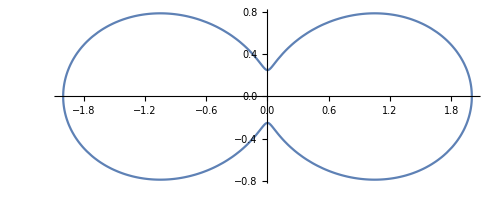

```mathematica
(* Figure 3.7 *) 
PolarPlot[ ( g[θ] /. ( eq3pt338  /. Equal-> Rule  ) ) , {θ,0,2π} ]
```

```mathematica
Clear[eq3pt341,R]
eq3pt341 = { 
x[t] == R Cos[ω t] , 
y[t] == R Cos[ι] Sin[ω t] , 
z[t] == R Sin[ι] Sin[ω t] 
} ;
eq3pt341  // TableForm
```

x[t]==R Cos[t ω]
y[t]==R Cos[ι] Sin[t ω]
z[t]==R Sin[ι] Sin[t ω]

```mathematica
Clear[X]
X =
 { x[t] , y[t] , z[t] } /. ( eq3pt341  /. Equal-> Rule )
```

{R Cos[t ω],R Cos[ι] Sin[t ω],R Sin[ι] Sin[t ω]}

```mathematica
(* I think this looks right *) 
Clear[eq3pt334]
eq3pt334 = 
Mab3 == μ Table[  X[[a]] X[[b]] X[[3]] , {a,1,2},{b,1,2} ]   ;
eq3pt334[[2]]// MatrixForm
```

(R^3 μ Cos[t ω]^2 Sin[ι] Sin[t ω] | R^3 μ Cos[ι] Cos[t ω] Sin[ι] Sin[t ω]^2
R^3 μ Cos[ι] Cos[t ω] Sin[ι] Sin[t ω]^2 | R^3 μ Cos[ι]^2 Sin[ι] Sin[t ω]^3)

```mathematica
(* Using the n on page 110 *) 
(* Equation 1.36 Page 9 for Λ *) 
(* Need to go back and change for 2-D *) 
Λ[n] // MatrixForm
```

((1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (-1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
(1/2)eq3pt334[[2]][[1,1]]-eq3pt334[[2]][[2,2]]
(-1/2)eq3pt334[[2]][[1,1]]-eq3pt334[[2]][[2,2]]
```

1/2 R^3 μ Cos[t ω]^2 Sin[ι] Sin[t ω]-R^3 μ Cos[ι]^2 Sin[ι] Sin[t ω]^3

-1/2 R^3 μ Cos[t ω]^2 Sin[ι] Sin[t ω]-R^3 μ Cos[ι]^2 Sin[ι] Sin[t ω]^3

```mathematica
Clear[eq3pt344]
eq3pt344 = 
({{(1/2)eq3pt334[[2]][[1,1]]-eq3pt334[[2]][[2,2]], eq3pt334[[2]][[1,2]]}, {eq3pt334[[2]][[2,1]], (-1/2)eq3pt334[[2]][[1,1]]-eq3pt334[[2]][[2,2]]}}) ;
eq3pt344  // MatrixForm
```

(1/2 R^3 μ Cos[t ω]^2 Sin[ι] Sin[t ω]-R^3 μ Cos[ι]^2 Sin[ι] Sin[t ω]^3 | R^3 μ Cos[ι] Cos[t ω] Sin[ι] Sin[t ω]^2
R^3 μ Cos[ι] Cos[t ω] Sin[ι] Sin[t ω]^2 | -1/2 R^3 μ Cos[t ω]^2 Sin[ι] Sin[t ω]-R^3 μ Cos[ι]^2 Sin[ι] Sin[t ω]^3)

```mathematica
(* Go back and redo this, not right and not finished *) 
Clear[eq3pt345a]
eq3pt345a = 
Simplify[Expand[D[ eq3pt344  , {t,3} ]]]   ;
eq3pt345a // MatrixForm
```

(-1/2 R^3 μ ω^3 Cos[t ω] Sin[ι] ((13+6 Cos[2 ι]) Cos[t ω]^2-(41+21 Cos[2 ι]) Sin[t ω]^2) | -1/4 R^3 μ ω^3 (13+27 Cos[2 t ω]) Sin[2 ι] Sin[t ω]
-1/4 R^3 μ ω^3 (13+27 Cos[2 t ω]) Sin[2 ι] Sin[t ω] | 1/8 R^3 μ ω^3 Cos[t ω] (4+30 Cos[2 ι]-27 Cos[2 (ι-t ω)]-27 Cos[2 (ι+t ω)]) Sin[ι])

## Chapter 4 (A few need to be moved)

```mathematica
Clear[eq4pt1]
eq4pt1 = 
ω^2== (G m)/ℛ^3
```

ω^2==(G m)/ℛ^3

```mathematica
Flatten[Solve[ eq4pt1 , ℛ ] ][[1]]
```

ℛ→(G^(1/3) m^(1/3))/ω^(2/3)

```mathematica
Clear[eq4pt2]
eq4pt2 = 
Mc == μ^(3/5) m^(2/5) == (m1 m2)^(3/5)/(m1 + m2)^(1/5)
```

Mc==m^(2/5) μ^(3/5)==(m1 m2)^(3/5)/(m1+m2)^(1/5)

```mathematica
PowerExpand[Flatten[Solve[ eq4pt2[[1;;2]] , μ ]][[1]] ]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

μ→Mc^(5/3)/m^(2/3)

```mathematica
eq3pt330
eq3pt330 /. Flatten[Solve[ eq4pt1 , ℛ ] ][[1]]
( eq3pt330 /. Flatten[Solve[ eq4pt1 , ℛ ] ][[1]]  ) /.PowerExpand[Flatten[Solve[ eq4pt2[[1;;2]] , μ ]][[1]] ]
```

(G ℛ^2 μ ω^2 (3+Cos[2 θ]) Cos[2 (ϕ+t ω)])/(c^4 r)

(G^(5/3) m^(2/3) μ ω^(2/3) (3+Cos[2 θ]) Cos[2 (ϕ+t ω)])/(c^4 r)

Solve::nongen: Solutions may not be valid for all values of parameters.

(G^(5/3) Mc^(5/3) ω^(2/3) (3+Cos[2 θ]) Cos[2 (ϕ+t ω)])/(c^4 r)

```mathematica
(* Redo equation 4.3 *)
```

```mathematica
Clear[eq4pt51]
eq4pt51 = 
a == ℛ/(1-ℯ^2)
```

a==ℛ/(1-ℯ^2)

```mathematica
Collect[ Expand[Flatten[Solve[ eq4pt51 , ℛ ] ][[1]]] ,a]
```

ℛ→a (1-ℯ^2)

```mathematica
Clear[eq4pt54]
eq4pt54 = 
r[t] == (a(1-ℯ^2))/(1+ℯ Cos[ψ[t] ])
```

r[t]==(a (1-ℯ^2))/(1+ℯ Cos[ψ[t]])

```mathematica
eq4pt54 /. Equal-> Rule
```

r[t]→(a (1-ℯ^2))/(1+ℯ Cos[ψ[t]])

```mathematica
Clear[eq4pt55] (* ℳ for mass - M for matrix *) 
eq4pt55 = 
ψ'[t] == (√(G ℳ ℛ))/r[t]^2
```

ψ'[t]==(√(G ℳ ℛ))/r[t]^2

```mathematica
eq4pt55  /. Equal-> Rule
```

ψ'[t]→(√(G ℳ ℛ))/r[t]^2

```mathematica
D[ eq4pt55 ,t ]  /. Equal-> Rule
```

ψ''[t]→-(2 √(G ℳ ℛ) r'[t])/r[t]^3

```mathematica
Clear[eq4pt59]
eq4pt59 = 
ω0^2== (G m)/a^3
```

ω0^2==(G m)/a^3

```mathematica
Flatten[Solve[ eq4pt59 , ω0]][[1]]
```

ω0→-(√G √m)/a^(3/2)

```mathematica
(*
Where to compare this calculation:
Problem Book In Relativity Page 497
Straumann Page
```

```mathematica
Clear[eq4pt65]
eq4pt65 = 
μ r^2({{Cos[ψ]^2, Sin[ψ] Cos[ψ]}, {Sin[ψ] Cos[ψ], Sin[ψ]^2}}) /. ψ-> ψ[t]   /. r-> r[t];
eq4pt65  // MatrixForm
```

(μ Cos[ψ[t]]^2 r[t]^2 | μ Cos[ψ[t]] r[t]^2 Sin[ψ[t]]
μ Cos[ψ[t]] r[t]^2 Sin[ψ[t]] | μ r[t]^2 Sin[ψ[t]]^2)

```mathematica
Clear[ellipticSecondMassMoment]
ellipticSecondMassMoment = 
eq4pt65  /. ( eq4pt54 /. Equal-> Rule  )   ;
ellipticSecondMassMoment // MatrixForm
```

((a^2 (1-ℯ^2)^2 μ Cos[ψ[t]]^2)/(1+ℯ Cos[ψ[t]])^2 | (a^2 (1-ℯ^2)^2 μ Cos[ψ[t]] Sin[ψ[t]])/(1+ℯ Cos[ψ[t]])^2
(a^2 (1-ℯ^2)^2 μ Cos[ψ[t]] Sin[ψ[t]])/(1+ℯ Cos[ψ[t]])^2 | (a^2 (1-ℯ^2)^2 μ Sin[ψ[t]]^2)/(1+ℯ Cos[ψ[t]])^2)

```mathematica
Clear[eq4pt66]
eq4pt66 = 
eq4pt65[[1,1]]  /. ( eq4pt54 /. Equal-> Rule  )
```

(a^2 (1-ℯ^2)^2 μ Cos[ψ[t]]^2)/(1+ℯ Cos[ψ[t]])^2

```mathematica
D[ eq4pt66 , t]  // Expand // Simplify
```

-(a^2 (-1+ℯ^2)^2 μ Sin[2 ψ[t]] ψ'[t])/(1+ℯ Cos[ψ[t]])^3

```mathematica
Clear[psiPrimeReplace] (* put in assumptions about size of ℯ *) 
psiPrimeReplace = 
( ( eq4pt55  /. Equal-> Rule )  /. ( eq4pt54  /. Equal-> Rule  )  ) /. Collect[ Expand[Flatten[Solve[ eq4pt51 , ℛ ] ][[1]]] ,a] // PowerExpand
```

ψ'[t]→(√G √ℳ (1+ℯ Cos[ψ[t]])^2)/(a^(3/2) (1-ℯ^2)^(3/2))

```mathematica
Clear[eq4pt67]
eq4pt67 = 
psiPrimeReplace
```

ψ'[t]→(√G √ℳ (1+ℯ Cos[ψ[t]])^2)/(a^(3/2) (1-ℯ^2)^(3/2))

```mathematica
D[ eq4pt66 , t]   /. psiPrimeReplace// Expand // Simplify
```

-(√a √G √(1-ℯ^2) √ℳ μ Sin[2 ψ[t]])/(1+ℯ Cos[ψ[t]])

```mathematica
Clear[psiDoublePrimeReplace]
psiDoublePrimeReplace = 
D[ psiPrimeReplace  , t ]  /. psiPrimeReplace
```

ψ''[t]→-(2 G ℯ ℳ (1+ℯ Cos[ψ[t]])^3 Sin[ψ[t]])/(a^3 (1-ℯ^2)^3)

```mathematica
Clear[Mdot]
Mdot = 
D[ ellipticSecondMassMoment  , t ]  /. psiPrimeReplace // Expand // Simplify  ;
Mdot // MatrixForm
```

(-(√a √G √(1-ℯ^2) √ℳ μ Sin[2 ψ[t]])/(1+ℯ Cos[ψ[t]]) | (√a √G √(1-ℯ^2) √ℳ μ (ℯ Cos[ψ[t]]+Cos[2 ψ[t]]))/(1+ℯ Cos[ψ[t]])
(√a √G √(1-ℯ^2) √ℳ μ (ℯ Cos[ψ[t]]+Cos[2 ψ[t]]))/(1+ℯ Cos[ψ[t]]) | (2 √a √G √(1-ℯ^2) √ℳ μ (ℯ+Cos[ψ[t]]) Sin[ψ[t]])/(1+ℯ Cos[ψ[t]]))

```mathematica
(* Done both ways - simply at each step or take two derivatives and simply at the end.  Both look wrong *) 
Clear[MdoubleDot]
MdoubleDot = 
D[ Mdot ,t ]  /. psiPrimeReplace // Expand // Simplify  ;
MdoubleDot// MatrixForm
```

((G ℳ μ (3 ℯ Cos[ψ[t]]+4 Cos[2 ψ[t]]+ℯ Cos[3 ψ[t]]))/(2 a (-1+ℯ^2)) | (G ℳ μ (4 Cos[ψ[t]]+ℯ (3+Cos[2 ψ[t]])) Sin[ψ[t]])/(a (-1+ℯ^2))
(G ℳ μ (4 Cos[ψ[t]]+ℯ (3+Cos[2 ψ[t]])) Sin[ψ[t]])/(a (-1+ℯ^2)) | -(G ℳ μ (7 ℯ Cos[ψ[t]]+4 Cos[2 ψ[t]]+ℯ (4 ℯ+Cos[3 ψ[t]])))/(2 a (-1+ℯ^2)))

```mathematica
Clear[MtripleDot]
MtripleDot = 
D[ MdoubleDot , t]  /. psiPrimeReplace // Expand // Simplify  ;
MtripleDot// MatrixForm
```

((G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (4+3 ℯ Cos[ψ[t]]) Sin[2 ψ[t]])/(a^(5/2) (1-ℯ^2)^(5/2)) | -(G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (5 ℯ Cos[ψ[t]]+8 Cos[2 ψ[t]]+3 ℯ Cos[3 ψ[t]]))/(2 a^(5/2) (1-ℯ^2)^(5/2))
-(G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (5 ℯ Cos[ψ[t]]+8 Cos[2 ψ[t]]+3 ℯ Cos[3 ψ[t]]))/(2 a^(5/2) (1-ℯ^2)^(5/2)) | -(G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (8 Cos[ψ[t]]+ℯ (5+3 Cos[2 ψ[t]])) Sin[ψ[t]])/(a^(5/2) (1-ℯ^2)^(5/2)))

```mathematica
Clear[eq4pt68]
eq4pt68 =
MtripleDot[[1,1]]
```

(G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (4+3 ℯ Cos[ψ[t]]) Sin[2 ψ[t]])/(a^(5/2) (1-ℯ^2)^(5/2))

```mathematica
Clear[eq4pt69]
eq4pt69 =
MtripleDot[[2,2]]
```

-(G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (8 Cos[ψ[t]]+ℯ (5+3 Cos[2 ψ[t]])) Sin[ψ[t]])/(a^(5/2) (1-ℯ^2)^(5/2))

```mathematica
Clear[eq4pt70]
eq4pt70 =
MtripleDot[[1,2]]
```

-(G^(3/2) ℳ^(3/2) μ (1+ℯ Cos[ψ[t]])^2 (5 ℯ Cos[ψ[t]]+8 Cos[2 ψ[t]]+3 ℯ Cos[3 ψ[t]]))/(2 a^(5/2) (1-ℯ^2)^(5/2))

```mathematica
(* Absolutely no idea yet if this is even close *) 
Clear[eq4pt72]
eq4pt72 = 
(G/(5 c^5))*(Sum[ MtripleDot[[i,j]] MtripleDot[[i,j]]  , {i,1,2},{j,1,2} ] - (1/3) Sum[( MtripleDot[[k,k]] )^2  , {k,1,2} ] ) // Expand // Simplify
```

-(ℳ^3 μ^2 (G+G ℯ Cos[ψ[t]])^4 (320+178 ℯ^2+640 ℯ Cos[ψ[t]]+167 ℯ^2 Cos[2 ψ[t]]+80 ℯ Cos[3 ψ[t]]+64 Cos[4 ψ[t]]+30 ℯ^2 Cos[4 ψ[t]]+48 ℯ Cos[5 ψ[t]]+9 ℯ^2 Cos[6 ψ[t]]))/(60 a^5 c^5 (-1+ℯ^2)^5)

```mathematica
(* Absolutely no idea yet if this is even close *) 
( 1/( ψ'[t] /. psiPrimeReplace) * eq4pt72  // Expand  // Simplify  ) /. ψ[t]-> ψ
```

(G^(7/2) ℳ^(5/2) (μ+ℯ μ Cos[ψ])^2 (320+178 ℯ^2+640 ℯ Cos[ψ]+167 ℯ^2 Cos[2 ψ]+80 ℯ Cos[3 ψ]+64 Cos[4 ψ]+30 ℯ^2 Cos[4 ψ]+48 ℯ Cos[5 ψ]+9 ℯ^2 Cos[6 ψ]))/(60 a^(7/2) c^5 (1-ℯ^2)^(7/2))

```mathematica
Clear[eq4pt74a] (* equation 4pt59 for ω0 *) 
eq4pt74a = 
 (ω0/(2 π)) *Integrate[ (( 1/( ψ'[t] /. psiPrimeReplace) * eq4pt72  // Expand  // Simplify  ) /. ψ[t]-> ψ )  , {ψ,0,2π} ]
```

(G^(7/2) (1280+3912 ℯ^2+523 ℯ^4) ℳ^(5/2) μ^2 ω0)/(240 a^(7/2) c^5 (1-ℯ^2)^(7/2))

```mathematica
(* This is wrong, but tantalizingly close.... find mistake *) 
(* Issue with Mass m and ℳ *) 
Clear[eq4pt74b] (* equation 4pt59 for ω0 *) 
eq4pt74b = 
eq4pt74a    /.  Flatten[Solve[ eq4pt59 , ω0]][[1]]    // FullSimplify
```

-(G^4 √m (1280+3912 ℯ^2+523 ℯ^4) ℳ^(5/2) μ^2)/(240 a^5 c^5 (1-ℯ^2)^(7/2))

```mathematica
Coefficient[ Expand[( eq4pt74a[[6]]  )/1280  ] , ℯ^2]
Coefficient[ Expand[( eq4pt74a[[6]]  )/1280  ] , ℯ^4]
```

489/160

523/1280

```mathematica
Clear[eq4pt201] (* Do this derivation later *) 
eq4pt201 = { 
I1 == (m/5)(b^2+c^2) , 
I2 == (m/5)(a^2+c^2) , 
I3 == (m/5)(a^2+b^2) 
} ;
 eq4pt201  // TableForm
```

I1==1/5 (b^2+c^2) m
I2==1/5 (a^2+c^2) m
I3==1/5 (a^2+b^2) m

```mathematica
(* Equation 4.208 equation  *) 
Clear[R]
R = 
({{Cos[t ω], Sin[t ω], 0}, {-Sin[t ω], Cos[t ω], 0}, {0, 0, 1}}) ;
R // MatrixForm
```

(Cos[t ω] | Sin[t ω] | 0
-Sin[t ω] | Cos[t ω] | 0
0 | 0 | 1)

```mathematica
Clear[ℐ] (* described under dquation 4.208 *) 
ℐ = 
({{I1, 0, 0}, {0, I2, 0}, {0, 0, I3}}) ;
ℐ // MatrixForm
```

(I1 | 0 | 0
0 | I2 | 0
0 | 0 | I3)

```mathematica
Clear[eq4pt210]
eq4pt210 = 
 Transpose[R] . ℐ . R   ;
eq4pt210 // MatrixForm
```

(I1 Cos[t ω]^2+I2 Sin[t ω]^2 | I1 Cos[t ω] Sin[t ω]-I2 Cos[t ω] Sin[t ω] | 0
I1 Cos[t ω] Sin[t ω]-I2 Cos[t ω] Sin[t ω] | I2 Cos[t ω]^2+I1 Sin[t ω]^2 | 0
0 | 0 | I3)

```mathematica
Clear[eq4pt211] (* Check to see if the first term RHS in book is actually 1 - find identity for ( I1 + I2 ) / 2 *) 
eq4pt211 = 
Collect[ TrigReduce[eq4pt210 [[1,1]] ] , Cos[2 ω t] ]
```

(I1+I2)/2+1/2 (I1-I2) Cos[2 t ω]

```mathematica
Clear[eq4pt212] (* Change trig identity later *) 
eq4pt212 = 
Collect[ TrigReduce[eq4pt210 [[1,2]]] , Sin[2 ω t] ]
```

1/2 (I1-I2) Sin[2 t ω]

```mathematica
Clear[eq4pt213] (* Check to see if the first term RHS in book is actually 1 - find identity for ( I1 + I2 ) / 2 *) 
eq4pt213 = 
Collect[ TrigReduce[eq4pt210 [[2,2]] ], Cos[2 ω t] ]
```

(I1+I2)/2+1/2 (-I1+I2) Cos[2 t ω]

```mathematica
Clear[eq4pt214] 
eq4pt214= 
eq4pt210[[3,3]]
```

I3

```mathematica
Clear[eq4pt216] (* constant term just looks strange *) 
eq4pt216 = 
M11[t] == - eq4pt211
```

M11[t]==1/2 (-I1-I2)-1/2 (I1-I2) Cos[2 t ω]

```mathematica
Clear[eq4pt217] (* constant term just looks strange *) 
eq4pt217 = 
M12[t] == - eq4pt212
```

M12[t]==-1/2 (I1-I2) Sin[2 t ω]

```mathematica
Clear[eq4pt218] (* constant term just looks strange *) 
eq4pt218 = 
M22[t] == Collect[ Expand[ - eq4pt213 ] , Cos[2 ω t] ]
```

M22[t]==-I1/2-I2/2+(I1/2-I2/2) Cos[2 t ω]

```mathematica
Clear[rigidBodySecondMassMoment] (* Other M's are constant , I just used zero *) 
rigidBodySecondMassMoment  = 
M /. { eq4pt216  /. Equal-> Rule } /. { eq4pt217  /. Equal-> Rule } /. { eq4pt218  /. Equal-> Rule } /. M13[t]-> 0 /. M23[t]-> 0  /. M33[t]-> 0  ;
rigidBodySecondMassMoment  // MatrixForm
```

(1/2 (-I1-I2)-1/2 (I1-I2) Cos[2 t ω] | -1/2 (I1-I2) Sin[2 t ω] | 0
-1/2 (I1-I2) Sin[2 t ω] | -I1/2-I2/2+(I1/2-I2/2) Cos[2 t ω] | 0
0 | 0 | 0)

```mathematica
Clear[rigidBodySecondMomentReplace]
rigidBodySecondMomentReplace = 
Table[ 
Flatten[D[ M , {t,2} ] ][[i]] -> 
Flatten[TrigReduce[D[ rigidBodySecondMassMoment , {t,2}] ]][[i]] , {i,1,9} ]   ;
rigidBodySecondMomentReplace// TableForm
```

M11''[t]→2 (I1 ω^2 Cos[2 t ω]-I2 ω^2 Cos[2 t ω])
M12''[t]→2 (I1 ω^2 Sin[2 t ω]-I2 ω^2 Sin[2 t ω])
M13''[t]→0
M12''[t]→2 (I1 ω^2 Sin[2 t ω]-I2 ω^2 Sin[2 t ω])
M22''[t]→-2 (I1 ω^2 Cos[2 t ω]-I2 ω^2 Cos[2 t ω])
M23''[t]→0
M13''[t]→0
M23''[t]→0
M33''[t]→0

```mathematica
Clear[eq4pt219] (* Figure out how to expand Cos[2ι] *) 
eq4pt219 = 
( eq3pt72a /. ϕ-> 0 /. θ -> ι  /. rigidBodySecondMomentReplace  // Expand )  // Simplify
```

(G (I1-I2) ω^2 (3+Cos[2 ι]) Cos[2 t ω])/(c^4 r)

```mathematica
(* Has to be a better way *) 
 eq4pt219[[6]]  
( ( eq4pt219[[6]]  // TrigExpand )    //.  Sin[ι]-> √(1 - Cos[ι]^2) )
```

3+Cos[2 ι]

2+2 Cos[ι]^2

```mathematica
Clear[eq4pt220]
eq4pt220 = 
( eq3pt72b/. ϕ-> 0 /. θ -> ι  /. rigidBodySecondMomentReplace  // Expand ) // Simplify
```

(4 G (I1-I2) ω^2 Cos[ι] Sin[2 t ω])/(c^4 r)

```mathematica
Clear[eq4pt221]
eq4pt221= 
ϵ == ((I1-I2)/I3)
```

ϵ==(I1-I2)/I3

```mathematica
(* Used for equation 4.223 *) 
Flatten[Solve[ eq4pt221 , I1 ] ][[1]]
Flatten[Solve[ eq4pt221 , I2 ] ][[1]]
```

I1→I2+I3 ϵ

I2→I1-I3 ϵ

```mathematica
eq4pt201 /. Equal-> Rule // TableForm
```

I1→1/5 (b^2+c^2) m
I2→1/5 (a^2+c^2) m
I3→1/5 (a^2+b^2) m

```mathematica
Clear[eq4pt222a]
eq4pt222a = 
eq4pt221 /. ( eq4pt201 /. Equal-> Rule  ) // Expand  // Simplify
```

ϵ==(-a^2+b^2)/(a^2+b^2)

```mathematica
(* Figure out this expansion later *) 
eq4pt222a[[2]]
```

(-a^2+b^2)/(a^2+b^2)

```mathematica
Clear[eq4pt222]
eq4pt222 = 
ϵ == ((b-a)/a)  ;
eq4pt222 /. Equal-> Rule
```

ϵ→(-a+b)/a

```mathematica
Clear[eq4pt223a]
eq4pt223a = 
eq4pt219  /. Flatten[Solve[ eq4pt221 , I1 ] ][[1]] /. ω -> 2 π frot /. frot -> fgw/2
```

(fgw^2 G I3 π^2 ϵ Cos[2 fgw π t] (3+Cos[2 ι]))/(c^4 r)

```mathematica
eq4pt223a [[1;;7]]
eq4pt223a[[8;;9]]
```

(fgw^2 G I3 π^2 ϵ)/(c^4 r)

Cos[2 fgw π t] (3+Cos[2 ι])

```mathematica
Clear[eq4pt223b]
eq4pt223b = 
eq4pt220  /. Flatten[Solve[ eq4pt221 , I1 ] ][[1]] /. ω -> 2 π frot /. frot -> fgw/2
```

(4 fgw^2 G I3 π^2 ϵ Cos[ι] Sin[2 fgw π t])/(c^4 r)

```mathematica
Clear[eq4pt224]
eq4pt224 = 
eq4pt223b[[1;;8]] ;

eq4pt224 
eq4pt223b[[9;;10]]
```

(4 fgw^2 G I3 π^2 ϵ)/(c^4 r)

Cos[ι] Sin[2 fgw π t]

```mathematica
Clear[rigidBodyThirdTimeDerivative]
rigidBodyThirdTimeDerivative = 
Table[ 
Flatten[D[ M , {t,3} ] ][[i]] -> 
Flatten[TrigReduce[D[ rigidBodySecondMassMoment , {t,3}] ]][[i]] , {i,1,9} ]   ;
rigidBodyThirdTimeDerivative // TableForm
```

M11^(3)[t]→-4 (I1 ω^3 Sin[2 t ω]-I2 ω^3 Sin[2 t ω])
M12^(3)[t]→4 (I1 ω^3 Cos[2 t ω]-I2 ω^3 Cos[2 t ω])
M13^(3)[t]→0
M12^(3)[t]→4 (I1 ω^3 Cos[2 t ω]-I2 ω^3 Cos[2 t ω])
M22^(3)[t]→4 (I1 ω^3 Sin[2 t ω]-I2 ω^3 Sin[2 t ω])
M23^(3)[t]→0
M13^(3)[t]→0
M23^(3)[t]→0
M33^(3)[t]→0

```mathematica
eq3pt76 /. rigidBodyThirdTimeDerivative   /. Flatten[Solve[ eq4pt221 , I2 ] ][[1]] // Expand  // Simplify 

(* Go back and see if setting t = 0 is a cheat *) 
Clear[eq4pt226]
eq4pt226 = 
( eq3pt76 /. rigidBodyThirdTimeDerivative   /. Flatten[Solve[ eq4pt221 , I2 ] ][[1]] // Expand  // Simplify  ) /. t-> 0
```

(16 G I3^2 ϵ^2 ω^6 (5+Cos[4 t ω]))/(15 c^5)

(32 G I3^2 ϵ^2 ω^6)/(5 c^5)

```mathematica
Clear[eq4pt227]
eq4pt227 = 
-eq4pt226
```

-(32 G I3^2 ϵ^2 ω^6)/(5 c^5)

```mathematica
Clear[eq4pt229]
eq4pt229 = 
({{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}}) . ({{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}}) . ({{Cos[β], Sin[β], 0}, {-Sin[β], Cos[β], 0}, {0, 0, 1}})  /. γ-> γ[t] /. α-> α[t] /. β-> β[t];
eq4pt229 // MatrixForm
```

(Cos[β[t]] Cos[γ[t]]-Cos[α[t]] Sin[β[t]] Sin[γ[t]] | Cos[γ[t]] Sin[β[t]]+Cos[α[t]] Cos[β[t]] Sin[γ[t]] | Sin[α[t]] Sin[γ[t]]
-Cos[α[t]] Cos[γ[t]] Sin[β[t]]-Cos[β[t]] Sin[γ[t]] | Cos[α[t]] Cos[β[t]] Cos[γ[t]]-Sin[β[t]] Sin[γ[t]] | Cos[γ[t]] Sin[α[t]]
Sin[α[t]] Sin[β[t]] | -Cos[β[t]] Sin[α[t]] | Cos[α[t]])

```mathematica
Clear[eq4pt244a]
eq4pt244a = 
Transpose[eq4pt229 ] . ℐ . eq4pt229   /. I2-> I1 // Expand // Simplify   ;
eq4pt244a // MatrixForm
```

(I1 Cos[β[t]]^2+1/2 (I1+I3+(I1-I3) Cos[2 α[t]]) Sin[β[t]]^2 | (I1-I3) Cos[β[t]] Sin[α[t]]^2 Sin[β[t]] | (-I1+I3) Cos[α[t]] Sin[α[t]] Sin[β[t]]
(I1-I3) Cos[β[t]] Sin[α[t]]^2 Sin[β[t]] | I1 Cos[α[t]]^2 Cos[β[t]]^2+I3 Cos[β[t]]^2 Sin[α[t]]^2+I1 Sin[β[t]]^2 | (I1-I3) Cos[α[t]] Cos[β[t]] Sin[α[t]]
(-I1+I3) Cos[α[t]] Sin[α[t]] Sin[β[t]] | (I1-I3) Cos[α[t]] Cos[β[t]] Sin[α[t]] | 1/2 (I1+I3+(-I1+I3) Cos[2 α[t]]))

```mathematica
(* The squares and double angles are on the wrong angles, see if this can be fixed *) 
Collect[ Expand[eq4pt244a[[1,1]]  ],{ I1,I3}]
```

I3 (1/2 Sin[β[t]]^2-1/2 Cos[2 α[t]] Sin[β[t]]^2)+I1 (Cos[β[t]]^2+1/2 Sin[β[t]]^2+1/2 Cos[2 α[t]] Sin[β[t]]^2)

```mathematica
(* This looks correct *) 
Collect[ Expand[eq4pt244a[[1,2]]  ],{ I1,I3}]  // Simplify
```

(I1-I3) Cos[β[t]] Sin[α[t]]^2 Sin[β[t]]

```mathematica
(* This looks correct *) 
Collect[ Expand[eq4pt244a[[2,2]]  ],{ I1,I3}]
```

I3 Cos[β[t]]^2 Sin[α[t]]^2+I1 (Cos[α[t]]^2 Cos[β[t]]^2+Sin[β[t]]^2)

```mathematica
(* This looks correct *) 
Collect[ Expand[eq4pt244a[[1,3]]],{ I1,I3}]   // Simplify
```

(-I1+I3) Cos[α[t]] Sin[α[t]] Sin[β[t]]

```mathematica
(* This looks correct *) 
Collect[ Expand[eq4pt244a[[2,3]]],{ I1,I3}]   // Simplify
```

(I1-I3) Cos[α[t]] Cos[β[t]] Sin[α[t]]

```mathematica
(* As close as I can get it *) 
(* Read why α is a constant  , from equation 4.237 *) 
( Collect[TrigExpand[ Expand[eq4pt244a[[3,3]]]],{ I1,I3}]   /. Cos[α[t]]-> √(1-Sin[α[t]]^2) // Expand  )
```

I3+I1 Sin[α[t]]^2-I3 Sin[α[t]]^2

```mathematica
Clear[eq4pt244]
eq4pt244 = { 
Collect[ Expand[eq4pt244a[[1,1]]  ],{ I1,I3}]  , 
Collect[ Expand[eq4pt244a[[1,2]]  ],{ I1,I3}]  // Simplify  , 
Collect[ Expand[eq4pt244a[[2,2]]  ],{ I1,I3}]   , 
Collect[ Expand[eq4pt244a[[1,3]]],{ I1,I3}]   // Simplify  , 
Collect[ Expand[eq4pt244a[[2,3]]],{ I1,I3}]   // Simplify  , 
( Collect[TrigExpand[ Expand[eq4pt244a[[3,3]]]],{ I1,I3}]   /. Cos[α[t]]-> √(1-Sin[α[t]]^2) // Expand  )  
} ;
eq4pt244  // TableForm
```

I3 (1/2 Sin[β[t]]^2-1/2 Cos[2 α[t]] Sin[β[t]]^2)+I1 (Cos[β[t]]^2+1/2 Sin[β[t]]^2+1/2 Cos[2 α[t]] Sin[β[t]]^2)
(I1-I3) Cos[β[t]] Sin[α[t]]^2 Sin[β[t]]
I3 Cos[β[t]]^2 Sin[α[t]]^2+I1 (Cos[α[t]]^2 Cos[β[t]]^2+Sin[β[t]]^2)
(-I1+I3) Cos[α[t]] Sin[α[t]] Sin[β[t]]
(I1-I3) Cos[α[t]] Cos[β[t]] Sin[α[t]]
I3+I1 Sin[α[t]]^2-I3 Sin[α[t]]^2

```mathematica
( eq4pt244a  /. α[t]-> α )   // MatrixForm
```

(I1 Cos[β[t]]^2+1/2 (I1+I3+(I1-I3) Cos[2 α]) Sin[β[t]]^2 | (I1-I3) Cos[β[t]] Sin[α]^2 Sin[β[t]] | (-I1+I3) Cos[α] Sin[α] Sin[β[t]]
(I1-I3) Cos[β[t]] Sin[α]^2 Sin[β[t]] | I1 Cos[α]^2 Cos[β[t]]^2+I3 Cos[β[t]]^2 Sin[α]^2+I1 Sin[β[t]]^2 | (I1-I3) Cos[α] Cos[β[t]] Sin[α]
(-I1+I3) Cos[α] Sin[α] Sin[β[t]] | (I1-I3) Cos[α] Cos[β[t]] Sin[α] | 1/2 (I1+I3+(-I1+I3) Cos[2 α]))

```mathematica
(* This is now M *) 
(-1)*( eq4pt244a  /. α[t]-> α )  // MatrixForm
```

(-I1 Cos[β[t]]^2-1/2 (I1+I3+(I1-I3) Cos[2 α]) Sin[β[t]]^2 | -((I1-I3) Cos[β[t]] Sin[α]^2 Sin[β[t]]) | -((-I1+I3) Cos[α] Sin[α] Sin[β[t]])
-((I1-I3) Cos[β[t]] Sin[α]^2 Sin[β[t]]) | -I1 Cos[α]^2 Cos[β[t]]^2-I3 Cos[β[t]]^2 Sin[α]^2-I1 Sin[β[t]]^2 | -((I1-I3) Cos[α] Cos[β[t]] Sin[α])
-((-I1+I3) Cos[α] Sin[α] Sin[β[t]]) | -((I1-I3) Cos[α] Cos[β[t]] Sin[α]) | 1/2 (-I1-I3-(-I1+I3) Cos[2 α]))

```mathematica
D[ (-1)*( eq4pt244a  /. α[t]-> α ) , {t,2} ]  // Expand  // Simplify
```

{{(I1-I3) Sin[α]^2 (2 Cos[2 β[t]] β'[t]^2+Sin[2 β[t]] β''[t]),(I1-I3) Sin[α]^2 (2 Sin[2 β[t]] β'[t]^2-Cos[2 β[t]] β''[t]),-((I1-I3) Cos[α] Sin[α] (Sin[β[t]] β'[t]^2-Cos[β[t]] β''[t]))},{(I1-I3) Sin[α]^2 (2 Sin[2 β[t]] β'[t]^2-Cos[2 β[t]] β''[t]),-((I1-I3) Sin[α]^2 (2 Cos[2 β[t]] β'[t]^2+Sin[2 β[t]] β''[t])),(I1-I3) Cos[α] Sin[α] (Cos[β[t]] β'[t]^2+Sin[β[t]] β''[t])},{-((I1-I3) Cos[α] Sin[α] (Sin[β[t]] β'[t]^2-Cos[β[t]] β''[t])),(I1-I3) Cos[α] Sin[α] (Cos[β[t]] β'[t]^2+Sin[β[t]] β''[t]),0}}

```mathematica
Clear[eq4pt245] (* I think this looks right *) 
eq4pt245 = 
D[ (-1)*( eq4pt244a  /. α[t]-> α  /. β[t]-> Ω t ) , {t,2} ]  // Expand // Simplify   ;
eq4pt245 // MatrixForm
```

(2 (I1-I3) Ω^2 Cos[2 t Ω] Sin[α]^2 | 2 (I1-I3) Ω^2 Sin[α]^2 Sin[2 t Ω] | (-I1+I3) Ω^2 Cos[α] Sin[α] Sin[t Ω]
2 (I1-I3) Ω^2 Sin[α]^2 Sin[2 t Ω] | -2 (I1-I3) Ω^2 Cos[2 t Ω] Sin[α]^2 | (I1-I3) Ω^2 Cos[α] Cos[t Ω] Sin[α]
(-I1+I3) Ω^2 Cos[α] Sin[α] Sin[t Ω] | (I1-I3) Ω^2 Cos[α] Cos[t Ω] Sin[α] | 0)

```mathematica
Clear[rigidBodySecondTimeDerivativeReplace]
rigidBodySecondTimeDerivativeReplace= 
Table[ 
Flatten[D[ M , {t,2} ] ][[i]] -> 
Flatten[D[ eq4pt245  , {t,2}] ][[i]] , {i,1,9} ]   ;
rigidBodySecondTimeDerivativeReplace // TableForm
```

M11''[t]→-8 (I1-I3) Ω^4 Cos[2 t Ω] Sin[α]^2
M12''[t]→-8 (I1-I3) Ω^4 Sin[α]^2 Sin[2 t Ω]
M13''[t]→-((-I1+I3) Ω^4 Cos[α] Sin[α] Sin[t Ω])
M12''[t]→-8 (I1-I3) Ω^4 Sin[α]^2 Sin[2 t Ω]
M22''[t]→8 (I1-I3) Ω^4 Cos[2 t Ω] Sin[α]^2
M23''[t]→-((I1-I3) Ω^4 Cos[α] Cos[t Ω] Sin[α])
M13''[t]→-((-I1+I3) Ω^4 Cos[α] Sin[α] Sin[t Ω])
M23''[t]→-((I1-I3) Ω^4 Cos[α] Cos[t Ω] Sin[α])
M33''[t]→0

```mathematica
Collect[ (eq3pt72a /. θ-> ι /. ϕ-> 0 /. rigidBodySecondTimeDerivativeReplace  // Expand)   , {Cos[Ω t] , Cos[2 Ω t] } ][[1]]  // Simplify 
Collect[ (eq3pt72a /. θ-> ι /. ϕ-> 0 /. rigidBodySecondTimeDerivativeReplace  // Expand)   , {Cos[Ω t] , Cos[2 Ω t] } ][[2]]  // Simplify
```

-(4 G (I1-I3) Ω^4 (3+Cos[2 ι]) Cos[2 t Ω] Sin[α]^2)/(c^4 r)

-(2 G (I1-I3) Ω^4 Cos[α] Cos[ι] Cos[t Ω] Sin[α] Sin[ι])/(c^4 r)

```mathematica
Clear[rigidBodyThirdTimeDerivativeReplace]
rigidBodyThirdTimeDerivativeReplace= 
Table[ 
Flatten[D[ M , {t,3} ] ][[i]] -> 
Flatten[D[(-1)*( eq4pt244a  /. α[t]-> α /. β[t]-> Ω t  )  , {t,3}] ][[i]]  // Expand // Simplify , {i,1,9} ]   ;
rigidBodyThirdTimeDerivativeReplace // TableForm
```

M11^(3)[t]→-4 (I1-I3) Ω^3 Sin[α]^2 Sin[2 t Ω]
M12^(3)[t]→4 (I1-I3) Ω^3 Cos[2 t Ω] Sin[α]^2
M13^(3)[t]→(-I1+I3) Ω^3 Cos[α] Cos[t Ω] Sin[α]
M12^(3)[t]→4 (I1-I3) Ω^3 Cos[2 t Ω] Sin[α]^2
M22^(3)[t]→4 (I1-I3) Ω^3 Sin[α]^2 Sin[2 t Ω]
M23^(3)[t]→(-I1+I3) Ω^3 Cos[α] Sin[α] Sin[t Ω]
M13^(3)[t]→(-I1+I3) Ω^3 Cos[α] Cos[t Ω] Sin[α]
M23^(3)[t]→(-I1+I3) Ω^3 Cos[α] Sin[α] Sin[t Ω]
M33^(3)[t]→0

```mathematica
(* I think this is correct if you expand the double angle *) 
Clear[eq4pt253]
eq4pt253 = 
 ( ( ( eq3pt76 /. rigidBodyThirdTimeDerivativeReplace  // Expand  ) /. t-> 0  ) // Simplify   ) /. Cos[2α]-> 1 - Sin[α]^2
```

-(G (I1-I3)^2 Ω^6 Sin[α]^2 (-17+15 (1-Sin[α]^2)))/(5 c^5)

```mathematica
LeviCivitaTensor[3][[i,k,l]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

SparseArray[…]⟦i,k,l⟧

```mathematica
Clear[eq4pt290] (* use ℳ for mass *) 
eq4pt290 = 
1/2 m z'[t]^2 - (G m ℳ)/z[t]== 0
```

-(G m ℳ)/z[t]+1/2 m z'[t]^2==0

```mathematica
Clear[eq4pt290a]
eq4pt290a = 
Rs == (2 G ℳ)/c^2
```

Rs==(2 G ℳ)/c^2

```mathematica
Flatten[Solve[eq4pt290a  ,  ℳ ] ][[1]]
```

ℳ→(c^2 Rs)/(2 G)

```mathematica
Flatten[Solve[ eq4pt290  , z'[t] ] ][[1]]

Clear[eq4pt291]
eq4pt291 = 
( Flatten[Solve[ eq4pt290  , z'[t] ] ][[1]]  /. Flatten[Solve[eq4pt290a  ,  ℳ ] ][[1]] // PowerExpand  ) /. Rule-> Equal
```

z'[t]→-(√2 √G √ℳ)/(√z[t])

z'[t]==-(c √Rs)/(√z[t])

```mathematica
(* Page 216 *) 
Clear[radialInfallSecondMassMoment]
radialInfallSecondMassMoment = 
({{0, 0, 0}, {0, 0, 0}, {0, 0, m z[t]^2}}) ;
radialInfallSecondMassMoment  // MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | m z[t]^2)

```mathematica
Clear[radialInfallThirdTimeDerivativeReplace]
radialInfallThirdTimeDerivativeReplace = 
Table[ 
Flatten[D[ M , {t,3} ] ][[i]] -> 
Flatten[D[radialInfallSecondMassMoment  , {t,3}] ][[i]]  // Expand // Simplify , {i,1,9} ]   ;
radialInfallThirdTimeDerivativeReplace // TableForm
```

M11^(3)[t]→0
M12^(3)[t]→0
M13^(3)[t]→0
M12^(3)[t]→0
M22^(3)[t]→0
M23^(3)[t]→0
M13^(3)[t]→0
M23^(3)[t]→0
M33^(3)[t]→2 m (3 z'[t] z''[t]+z[t] z^(3)[t])

```mathematica
(* write the 8 as 2*2^2 *) 
Clear[eq4pt292]
eq4pt292 = 
eq3pt76 /.radialInfallThirdTimeDerivativeReplace
```

(8 G m^2 (3 z'[t] z''[t]+z[t] z^(3)[t])^2)/(15 c^5)

```mathematica
D[ eq4pt291 , t ] 
( D[ eq4pt291 , t ] /.(  eq4pt291  /. Equal-> Rule ) ) /. Equal-> Rule
```

z''[t]==(c √Rs z'[t])/(2 z[t]^(3/2))

z''[t]→-(c^2 Rs)/(2 z[t]^2)

```mathematica
D[ ( ( D[ eq4pt291 , t ] /.(  eq4pt291  /. Equal-> Rule ) ) /. Equal-> Rule  ) , t ] 
D[ ( ( D[ eq4pt291 , t ] /.(  eq4pt291  /. Equal-> Rule ) ) /. Equal-> Rule  ) , t ]  /. (eq4pt291  /. Equal-> Rule )
```

z^(3)[t]→(c^2 Rs z'[t])/z[t]^3

z^(3)[t]→-(c^3 Rs^(3/2))/z[t]^(7/2)

```mathematica
Clear[zDerivativeReplace]
zDerivativeReplace = { 
eq4pt291  /. Equal-> Rule , 
( D[ eq4pt291 , t ] /.(  eq4pt291  /. Equal-> Rule ) ) /. Equal-> Rule  , 
D[ ( ( D[ eq4pt291 , t ] /.(  eq4pt291  /. Equal-> Rule ) ) /. Equal-> Rule  ) , t ]  /. (eq4pt291  /. Equal-> Rule ) 
} ;
zDerivativeReplace // TableForm
```

z'[t]→-(c √Rs)/(√z[t])
z''[t]→-(c^2 Rs)/(2 z[t]^2)
z^(3)[t]→-(c^3 Rs^(3/2))/z[t]^(7/2)

```mathematica
eq4pt292 
eq4pt292 /. zDerivativeReplace 
( eq4pt292 /. zDerivativeReplace  ) dt  (* This is the integrand for equation 4.293 *) 
( ( eq4pt292 /. zDerivativeReplace  ) dt  ) /. dt-> (dz/z'[t]) 
( ( ( eq4pt292 /. zDerivativeReplace  ) dt  ) /. dt-> (dz/z'[t])  ) /. zDerivativeReplace  
(( ( ( eq4pt292 /. zDerivativeReplace  ) dt  ) /. dt-> (dz/z'[t])  ) /. zDerivativeReplace   ) /. z[t]-> z 

Clear[eq4pt294a]
eq4pt294a = 
((((( ( ( eq4pt292 /. zDerivativeReplace  ) dt  ) /. dt-> (dz/z'[t])  ) /. zDerivativeReplace   ) /. z[t]-> z ) /. (z-> u Rs  ))/.  dz-> Rs du )  // PowerExpand (* This is the integrand for equation 4.294 - minus sign interchanges limit of integration  *)
```

(8 G m^2 (3 z'[t] z''[t]+z[t] z^(3)[t])^2)/(15 c^5)

(2 c G m^2 Rs^3)/(15 z[t]^5)

(2 c dt G m^2 Rs^3)/(15 z[t]^5)

(2 c dz G m^2 Rs^3)/(15 z[t]^5 z'[t])

-(2 dz G m^2 Rs^(5/2))/(15 z[t]^(9/2))

-(2 dz G m^2 Rs^(5/2))/(15 z^(9/2))

-(2 du G m^2)/(15 Rs u^(9/2))

```mathematica
Coefficient[ eq4pt294a , du ]
```

-(2 G m^2)/(15 Rs u^(9/2))

```mathematica
(* Remember, R is a rotation matrix somewhere so we use ℛ here *) 

Clear[eq4pt294]
 eq4pt294 = 
Integrate[ (-1)*Coefficient[ eq4pt294a , du ] , { u , (ℛ/Rs), ∞} ]
```

ConditionalExpression[(4 G m^2)/(105 Rs (ℛ/Rs)^(7/2)), Sign[ℛ]/Sign[Rs]≠-1||ℛ/Rs∉ℝ]

```mathematica
eq4pt294  /. ℛ-> Rs 

Clear[eq4pt295]
eq4pt295 = { 
( eq4pt294  /. ℛ-> Rs )  /. Rs-> ((2 G ℳ)/c^2) , 
( eq4pt294  /. ℛ-> Rs )  /. Rs-> ((2 G ℳ)/c^2)  // N 
} ;
eq4pt295 [[1]]
eq4pt295 [[2]]
```

(4 G m^2)/(105 Rs)

(2 c^2 m^2)/(105 ℳ)

(0.0190476 c^2 m^2)/ℳ

```mathematica
Clear[eq4pt379]
eq4pt379 = 
x[β] == a (Cos[u] - ℯ )
```

x[β]==a (-ℯ+Cos[u])

```mathematica
Clear[eq4pt380]
eq4pt380 = 
y[β] == b Sin[u]
```

y[β]==b Sin[u]

```mathematica
Clear[n,ℯ,u]
```

```mathematica
(* Should be equation 4.387 *)
Integrate[ Cos[n u - z Sin[u]] , {u,0,π},
Assumptions -> n ∈ Integers  &&  u  ∈ Reals  &&  z  ∈ Reals   ]
```

Integrate[Cos[n u-z Sin[u]],{u,0,π},Assumptions→n∈ℤ&&u∈ℝ&&z∈ℝ]

```mathematica
(* Should be Subscript[a, n]  page 233*) 
Integrate[ Cos[ (n-1) u - n ℯ Sin[u]] - Cos[(n+1)u - n ℯ Sin[u] ] , {u,0,π}  , 
Assumptions -> n ∈ Integers  &&  ℯ ∈ Reals   &&  u  ∈ Reals]
```

Integrate[Cos[(-1+n) u-n ℯ Sin[u]]-Cos[(1+n) u-n ℯ Sin[u]],{u,0,π},Assumptions→n∈ℤ&&ℯ∈ℝ]

```mathematica
(* Should be Subscript[b, n]  page 234 *) 
Integrate[ Cos[u] Cos[n u - n ℯ Sin[u] ]  , {u,0,π} ,
 Assumptions -> n ∈ Integers  &&  ℯ ∈ Reals   &&  u  ∈ Reals]
```

Integrate[Cos[u] Cos[n u-n ℯ Sin[u]],{u,0,π},Assumptions→n∈ℤ&&ℯ∈ℝ&&u∈ℝ]

## Chapter 8

```mathematica
Clear[eq8pt70]
eq8pt70 = 
ℒ == 1/2 m0 ξ0'[t]^2+ 1/2 mt ξt'[t]^2 - V
```

ℒ==-V+1/2 m0 ξ0'[t]^2+1/2 mt ξt'[t]^2

```mathematica
Clear[eq8pt71]
eq8pt71 = 
V == 1/2 m0 ω0^2 ξ0[t]^2 + 1/2 mt ωt^2 ( ξt[t]-ξ0[t])^2
```

V==1/2 m0 ω0^2 ξ0[t]^2+1/2 mt ωt^2 (-ξ0[t]+ξt[t])^2

```mathematica
eq8pt70  /. (eq8pt71  /. Equal-> Rule )
```

ℒ==-1/2 m0 ω0^2 ξ0[t]^2-1/2 mt ωt^2 (-ξ0[t]+ξt[t])^2+1/2 m0 ξ0'[t]^2+1/2 mt ξt'[t]^2

```mathematica
Clear[ℒ]
ℒ = eq8pt70[[2]]  /. (eq8pt71  /. Equal-> Rule )  ;
Clear[q]
q = { ξ0[t] , ξt[t] } ;
Clear[eom]
eom = EulerEquations[ℒ,q,t]  ;
eom // TableForm
```

-m0 ω0^2 ξ0[t]+mt ωt^2 (-ξ0[t]+ξt[t])-m0 ξ0''[t]==0
mt (ωt^2 ξ0[t]-ωt^2 ξt[t]-ξt''[t])==0

```mathematica
Clear[intermediateEOM]
intermediateEOM = 
( ( Flatten[Solve[ eom , { ξ0''[t] , ξt''[t] } ] ] /. mt-> μ m0  )  // Expand // Apart // Expand   )  /. Rule-> Equal   ;
intermediateEOM // TableForm
```

ξ0''[t]==-ω0^2 ξ0[t]-μ ωt^2 ξ0[t]+μ ωt^2 ξt[t]
ξt''[t]==ωt^2 ξ0[t]-ωt^2 ξt[t]

```mathematica
Clear[eq8pt72]
eq8pt72 = 
Collect[ intermediateEOM [[1]][[1]]-intermediateEOM [[1]][[2]]  , μ ωt^2 ] == (F0/m0)
```

ω0^2 ξ0[t]+μ ωt^2 (ξ0[t]-ξt[t])+ξ0''[t]==F0/m0

```mathematica
Clear[eq8pt73]
eq8pt73 = 
Collect[ intermediateEOM [[2]][[1]]-intermediateEOM [[2]][[2]]  , ωt^2]== (Ft/mt)
```

ωt^2 (-ξ0[t]+ξt[t])+ξt''[t]==Ft/mt

```mathematica
FourierTransform[ eq8pt72[[1]], t ,ω ]  // TraditionalForm
```

ℱ_t[μ ωt^2 (ξ0(t)-ξt(t))+ξ0''(t)+ω0^2 ξ0(t)](ω)

```mathematica
FourierTransform[f[t],t,ω] // TraditionalForm
FourierTransform[f'[t],t,ω] // TraditionalForm
FourierTransform[f''[t],t,ω] // TraditionalForm
```

ℱ_t[f(t)](ω)

-ⅈ ω (ℱ_t[f(t)](ω))

-ω^2 (ℱ_t[f(t)](ω))

## Chapter 9

```mathematica
Clear[eq9pt131]
eq9pt131 = 
({{SubPlus[h], Subscript[h,x], 0}, {Subscript[h,x], -SubPlus[h], 0}, {0, 0, 0}}) ;
eq9pt131  // MatrixForm
```

(h_+ | h_x | 0
h_x | -h_+ | 0
0 | 0 | 0)

```mathematica
Clear[eq9pt132]
eq9pt132 = 
({{Cos[ϕ], Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}}) . ({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}})   ;
eq9pt132  // MatrixForm
```

(Cos[θ] Cos[ϕ] | Sin[ϕ] | Cos[ϕ] Sin[θ]
-Cos[θ] Sin[ϕ] | Cos[ϕ] | -Sin[θ] Sin[ϕ]
-Sin[θ] | 0 | Cos[θ])

```mathematica
Clear[eq9pt132a]
eq9pt132a = 
Table[ Sum[ eq9pt132[[i,k]] eq9pt132[[j,l]] eq9pt131[[k,l]] , {k,1,3},{l,1,3} ] , {i,1,3},{j,1,3} ]  // Expand // Simplify   ;
Clear[eq9pt132]
eq9pt132a // MatrixForm
```

((Cos[θ]^2 Cos[ϕ]^2-Sin[ϕ]^2) h_++Cos[θ] Sin[2 ϕ] h_x | -1/4 (3+Cos[2 θ]) Sin[2 ϕ] h_++Cos[θ] Cos[2 ϕ] h_x | -Sin[θ] (Cos[θ] Cos[ϕ] h_++Sin[ϕ] h_x)
-1/4 (3+Cos[2 θ]) Sin[2 ϕ] h_++Cos[θ] Cos[2 ϕ] h_x | (-Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2) h_+-2 Cos[θ] Cos[ϕ] Sin[ϕ] h_x | Sin[θ] (Cos[θ] Sin[ϕ] h_+-Cos[ϕ] h_x)
-Sin[θ] (Cos[θ] Cos[ϕ] h_++Sin[ϕ] h_x) | Sin[θ] (Cos[θ] Sin[ϕ] h_+-Cos[ϕ] h_x) | Sin[θ]^2 h_+)

```mathematica
Clear[eq9pt133]
eq9pt133 = 
eq9pt132a[[1,1]]
```

(Cos[θ]^2 Cos[ϕ]^2-Sin[ϕ]^2) h_++Cos[θ] Sin[2 ϕ] h_x

```mathematica
Clear[eq9pt134]
eq9pt134 = 
eq9pt132a[[2,2]]
```

(-Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2) h_+-2 Cos[θ] Cos[ϕ] Sin[ϕ] h_x

```mathematica
Clear[eq9pt135a]
eq9pt135a = 
Collect[ ( ( ( eq9pt133 - eq9pt134 ) /2) // Expand ) , { SubPlus[h] , Subscript[h,x] } ]
```

(Cos[ϕ]^2/2+1/2 Cos[θ]^2 Cos[ϕ]^2-Sin[ϕ]^2/2-1/2 Cos[θ]^2 Sin[ϕ]^2) h_++(Cos[θ] Cos[ϕ] Sin[ϕ]+1/2 Cos[θ] Sin[2 ϕ]) h_x

```mathematica
(* This looks wrong and I'm tired *) 
Clear[eq9pt135]
eq9pt135 = 
(eq9pt135a[[1]] // Simplify )+(eq9pt135a[[2]] // Simplify )
```

1/4 (3+Cos[2 θ]) Cos[2 ϕ] h_++Cos[θ] Sin[2 ϕ] h_x

## Chapter 12 in Volume 2

```mathematica
(* 
In volume 2 start with equation 10.30 page 35  stress energy tensor of perfect fluid
*)
```

```mathematica
Clear[eq12pt261]
eq12pt261 = 
ξ''[t] + γ0 ξ'[t] + ω0^2 ξ[t] == f[t]
```

ω0^2 ξ[t]+γ0 ξ'[t]+ξ''[t]==f[t]

```mathematica
(* Need to look up tutorial on this *) 
FourierTransform[ eq12pt261[[1,3]]   , t , ω ] // TraditionalForm
FourierTransform[ eq12pt261[[2]]  , t , ω ] // TraditionalForm
```

-ω^2 (ℱ_t[ξ(t)](ω))

ℱ_t[f(t)](ω)